```mathematica
especies= 3;
metabolitos= 4;
```

```mathematica
n=especies;
m=metabolitos;
```

```mathematica
H = Table[RandomReal[{0.1,1}],m];
μ = Table[RandomReal[{0.01,0.1}],m];
δ = Table[RandomReal[{0.01,0.1}],n];
S = Table[RandomReal[5],m];
ciC = Table[RandomReal[5],m];
ciX = Table[RandomReal[5],n];
```

```mathematica
V = {
	{0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]}
	};
W = {
	{RandomReal[1],0,0},
	{RandomReal[1],0,0},
	{0,RandomReal[1],0},
	{0,RandomReal[1],0}
};
```

```mathematica
V//MatrixForm;
```

```mathematica
W//MatrixForm;
```

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[m];
x[t_] = speciesGen[n];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g =Table[ G[V⟦;;,i⟧,c[t]],{i,1,n}];
```

```mathematica
r = Table[R[i],{i,1,m}];
```

```mathematica
rr=DiagonalMatrix[r];
```

```mathematica
μμ= DiagonalMatrix[μ];
```

```mathematica
δδ=DiagonalMatrix[δ];
```

```mathematica
gg =DiagonalMatrix[g];
```

```mathematica
μc= μμ.c[t];
```

```mathematica
gδ=gg-δδ;
```

```mathematica
Wxr=(W.x[t]).rr;
```

```mathematica
Vxr=(V.x[t]).rr;
```

```mathematica
xgδ=x[t].gδ;
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +Wxr⟦i⟧-Vxr⟦i⟧-(μc⟦i⟧),{i,1,Length[c[t]]}]
eqX = Table[x'[t]⟦i⟧==xgδ⟦i⟧,{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

{c1'[t]==3.5684-0.0882833 c1[t]+(0.962851 c1[t] x1[t])/(0.626909+c1[t])-(c1[t] (0.100894 x2[t]+0.240058 x3[t]))/(0.626909+c1[t]),c2'[t]==0.635529-0.095672 c2[t]+(0.592092 c2[t] x1[t])/(0.412676+c2[t])-(0.775149 c2[t] x3[t])/(0.412676+c2[t]),c3'[t]==1.80399-0.0156463 c3[t]+(0.661508 c3[t] x2[t])/(0.294589+c3[t])-(0.0371966 c3[t] x3[t])/(0.294589+c3[t]),c4'[t]==0.778414-0.0494516 c4[t]+(0.712776 c4[t] x2[t])/(0.640589+c4[t])-(0.297013 c4[t] x3[t])/(0.640589+c4[t])}

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,10000}];
```

```mathematica
varc[t_]=Flatten[{c[t]}];
varx[t_] =Flatten[{x[t]}];
```

```mathematica
prueba=NDSolve[sistema, varc[t],{t,0,100}];
try= NDSolve[sistema, varx[t],{t,0,100}];
```

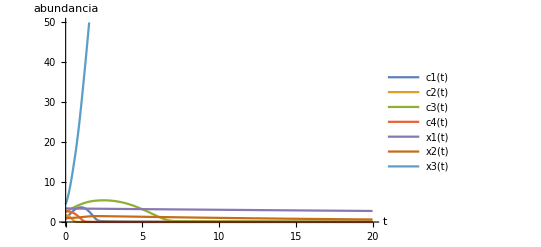

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,20},PlotLegends->vars[t],PlotRange->{0,50}, AxesLabel->{"t","abundancia"}]
```

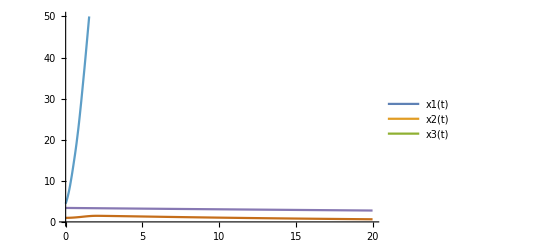

```mathematica
Plot[Evaluate[vars[t]/.try],{t,0,20},PlotLegends->varx[t],PlotRange->{0,50}]
```

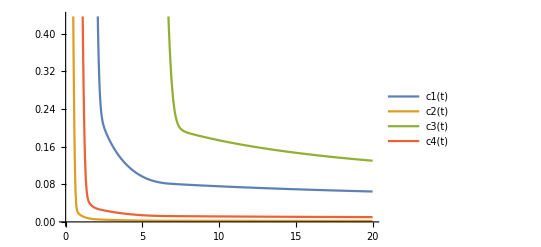

```mathematica
Plot[Evaluate[vars[t]/.prueba],{t,0,20},PlotLegends->varc[t]]
```

```mathematica
((V-W).x[t]);
```